```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Perturbation

```mathematica
$Assumptions= And[t∈Reals,r>0,r<1,ω>0];
```

```mathematica
Φ=Exp[-ⅈ*ω*t]*ϕ[r]
```

ⅇ^(-ⅈ t ω) ϕ[r]

```mathematica
f[r_]=1-r^2;
f2[r_]=(f[r] r^(d-1)ϕ'[r])//FullSimplify;
SEstep1 = -r^(1-d)f2'[r] //FullSimplify;
SEstep2 = Collect[SEstep1,{ϕ''[r],ϕ'[r],ϕ[r]},Simplify]+((l(l+d-2))/r^2-ω^2/f[r])ϕ[r]
```

((l (-2+d+l))/r^2-ω^2/(1-r^2)) ϕ[r]+((1-d)/r+r+d r) ϕ'[r]+(-1+r^2) ϕ''[r]

```mathematica
Solution1=Values[DSolve[SEstep2==0,ϕ[r],r]][[1]][[1]]//FullSimplify
```

((-r)^-l (ⅈ r)^-d (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) (-r^2 C[2] Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]+(-1)^l ⅈ^d r^(d+2 l) C[1] Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]))/(√(1-r^2))

```mathematica
SolutionR=(1-r^2)^((-ⅈ ω)/2)r^l Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]
SolutionNR=(1-r^2)^((-ⅈ ω)/2)r^(2-d-l)Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]
```

r^l (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]

r^(2-d-l) (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]

```mathematica
OriginBehaviour=Series[C1*SolutionR+C2*SolutionNR,{r,0,2}]//FullSimplify
```

r^(-d-l) (C2 r^2+O[r]^3)+r^l (C1+(C1 (l (d+l)-ω^2) r^2)/(2 (d+2 l))+O[r]^3)

```mathematica
Normal[Series[SolutionR,{r,1,0}]]//FullSimplify//Expand
```

(π (2-2 r)^(-(ⅈ ω)/2) Csch[π ω] Gamma[d/2+l])/(ω Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])+(π (2-2 r)^((ⅈ ω)/2) Csch[π ω] Gamma[d/2+l])/(ω Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])

```mathematica
BoundaryBehaviour=Normal[Series[C[1]SolutionR,{r,1,0}]]/.C[1]->C[1]/(π Csch[π ω] Gamma[d/2+l]/ω)//FullSimplify//Expand
```

((2-2 r)^(-(ⅈ ω)/2) C[1])/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])+((2-2 r)^((ⅈ ω)/2) C[1])/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])

```mathematica
Q1=1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])// FullSimplify
```

1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])

```mathematica
P1=1/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])//FullSimplify
```

1/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])

```mathematica
alpha=Arg[P1]//FullSimplify
beta=Arg[Q1]//FullSimplify
```

Arg[1/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])]

Arg[1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])]

```mathematica
p[s_, β_]=(1+α)Gamma[(2+β)/(1+α)]^(1+β)/Gamma[(1+β)/(1+α)]^(2+β)s^β Exp[-s^(α+1)Gamma[(2+β)/(1+α)]^(1+α)/Gamma[(1+β)/(1+α)]^(1+α)]
```

ⅇ^(-s^(1+α) Gamma[(1+β)/(1+α)]^(-1-α) Gamma[(2+β)/(1+α)]^(1+α)) s^β (1+α) Gamma[(1+β)/(1+α)]^(-2-β) Gamma[(2+β)/(1+α)]^(1+β)

### Quantization of Omega

Sigma=0

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,	
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.l->i/.d->3,{ω,0.00015},WorkingPrecision->300]]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

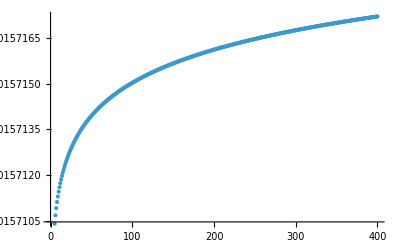

```mathematica
ListPlot[OmegaQuantization]
```

```mathematica
Export["DATAσ0.dat",OmegaQuantization]
```

DATAσ0.dat

```mathematica
Export["STATIC_SIGMA0.dat",Transpose[{Range[400],OmegaQuantization}]]
```

STATIC_SIGMA0.dat

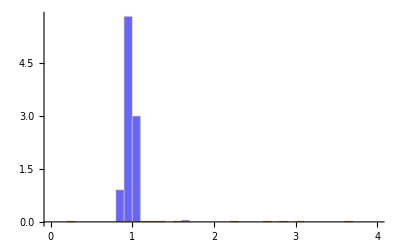

```mathematica
cumulativeDOS=Range[Length[OmegaQuantization]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantization,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantization];
spacings=Differences[Sort[unfoldedE]];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.017/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationtwo,Value[[1]]];
];
```

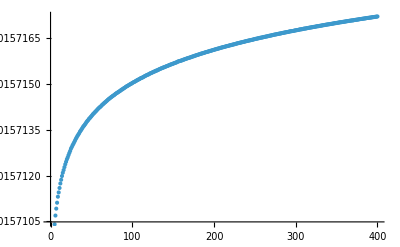

```mathematica
ListPlot[OmegaQuantizationtwo]
```

```mathematica
Export["STATIC_SIGMA05.dat",Transpose[{Range[400],OmegaQuantizationtwo}]]
```

STATIC_SIGMA05.dat

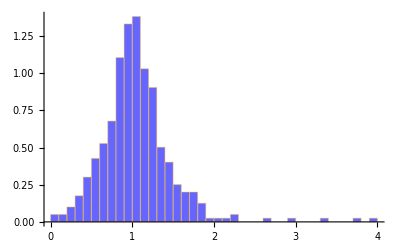

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationtwo]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationtwo],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationtwo]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

Sigma=0

```mathematica
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,	
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.l->i/.d->3,{ω,0.00015},WorkingPrecision->300]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
]
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationBeta,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta];
spacings=Differences[Sort[unfoldedE]];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts0}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
```

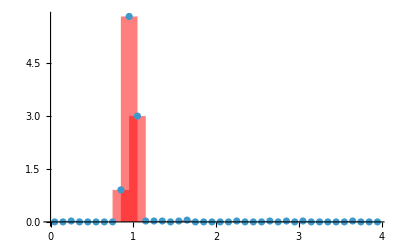

```mathematica
ListPlot[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0}],PlotRange->All,Filling->Axis,FillingStyle->Directive[Thickness[0.03],Opacity[0.5],Red]]
```

```mathematica
Export["STATIC_HISTOGRAM0.dat",Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0}]];
```

Sigma=0.017

```mathematica
cumulativebinCounts=0;
For[n=1,n<=100,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.017/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts0017}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts0017;

Echo[n]
];
binCounts0017 = cumulativebinCounts/100;
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

```mathematica
fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}, binCounts0017}],p[s, β]/.α->1,β,s]
```

FittedModel[…]

```mathematica
fit["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
β | 4.07351 | 0.216117 | 18.8486 | 3.41106×10^-21

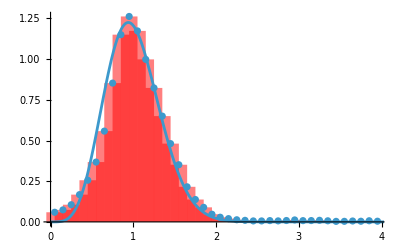

```mathematica
Show[{ListPlot[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0017}],PlotRange->All,Filling->Axis,FillingStyle->Directive[Thickness[0.03],Opacity[0.5],Red]],Plot[p[s,4]/.α->1,{s,0,6},PlotRange->All]}]
```

```mathematica
Export["STATIC_HISTOGRAM0017.dat",Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0017}]];
```

Sigma=0.024

```mathematica
cumulativebinCounts=0;
For[n=1,n<=100,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.023/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts0024}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts0024;

Echo[n]
];
binCounts0024 = cumulativebinCounts/100;
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

```mathematica
fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}, binCounts0024}],p[s, β]/.α->1,β,s];
```

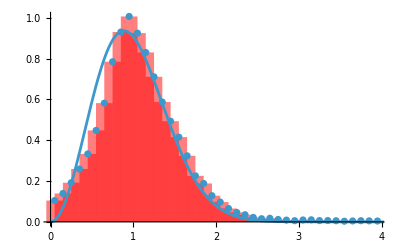

```mathematica
Show[{ListPlot[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0024}],PlotRange->All,Filling->Axis,FillingStyle->Directive[Thickness[0.03],Opacity[0.5],Red]],Plot[p[s,2]/.α->1,{s,0,6}]}]
```

```mathematica
Export["STATIC_HISTOGRAM0024.dat",Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0024}]];
```

Sigma=0.030

```mathematica
cumulativebinCounts=0;
For[n=1,n<=100,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.0302/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts0030}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts0030;

Echo[n]
];
binCounts0030 = cumulativebinCounts/100;
```

```mathematica
fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}, binCounts0030}],p[s, β]/.α->1,β,s];
```

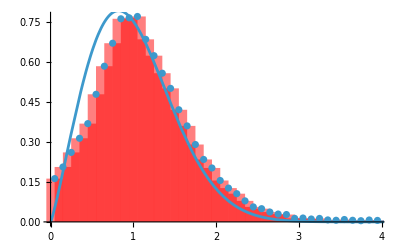

```mathematica
Show[{ListPlot[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0030}],PlotRange->All,Filling->Axis,FillingStyle->Directive[Thickness[0.03],Opacity[0.5],Red]],Plot[p[s,1.17955]/.α->1,{s,0,6}]}]
```

```mathematica
Export["STATIC_HISTOGRAM0030.dat",Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts0030}]];
```

Sigma=0.5

```mathematica
cumulativebinCounts=0;
For[n=1,n<=100,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.5/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationBeta,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta];
spacings=Differences[Sort[unfoldedE]];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts05}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts05;

Echo[n]
];
binCounts05 = cumulativebinCounts/100;
```

```mathematica
fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95}, binCounts05}],p[s, β]/.α->β,β,s];
```

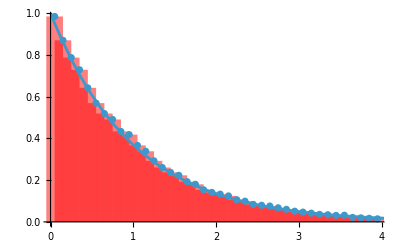

```mathematica
Show[{ListPlot[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts05}],PlotRange->All,Filling->Axis,FillingStyle->Directive[Thickness[0.03],Opacity[0.5],Red]],Plot[p[s,0]/.α->0,{s,0,6},PlotRange->All]}]
```

```mathematica
Export["STATIC_HISTOGRAM05.dat",Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts05}]];
```

### Estimation of beta

```mathematica
betas2={};
For[j=1,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.014+j*0.001)/Sqrt[i]],1] /.l->i /. d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->1,β,s];

AppendTo[betas2,Values[fit["BestFitParameters"]][[1]]];
Echo[betas2]
]
Export["BETA_SIGMA0_d2.dat",Transpose[{Array[0.014+#*0.001&,20],betas2}]]
```

BETA_SIGMA0_d2.dat

```mathematica
betas3={};
For[j=1,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.014+j*0.001)/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->1,β,s];

AppendTo[betas3,Values[fit["BestFitParameters"]][[1]]];
Echo[betas3]
]
Export["BETA_SIGMA0_d3.dat",Transpose[{Array[0.014+#*0.001&,20],betas3}]]
```

{5.1485,4.52594,4.0226,3.61429,3.14039,2.87249,2.55917,2.26182,2.04981,1.83913,1.64226,1.52932,1.32593,1.19529,1.08994,0.981925,0.893407,0.822459,0.727832,0.642296}

BETA_SIGMA0_d3.dat

```mathematica
betas4={};
For[j=1,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.014+j*0.001)/Sqrt[i]],1] /.l->i /. d->4,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->1,β,s];

AppendTo[betas4,Values[fit["BestFitParameters"]][[1]]];
Echo[betas4]
]
Export["BETA_SIGMA0_d4.dat",Transpose[{Array[0.014+#*0.001&,20],betas4}]]
```

BETA_SIGMA0_d4.dat

```mathematica
betas2
betas3
betas4
```

{5.1524,4.51057,3.95617,3.60485,3.22392,2.85079,2.56926,2.31093,2.10511,1.84943,1.70568,1.49546,1.37554,1.20969,1.08698,0.979099,0.890755,0.811511,0.717901,0.667341}

{5.1485,4.52594,4.0226,3.61429,3.14039,2.87249,2.55917,2.26182,2.04981,1.83913,1.64226,1.52932,1.32593,1.19529,1.08994,0.981925,0.893407,0.822459,0.727832,0.642296}

{5.23466,4.59299,4.0117,3.5556,3.18581,2.80208,2.51454,2.27642,2.07296,1.83438,1.65888,1.48706,1.34263,1.16338,1.06693,0.933585,0.867869,0.761806,0.723823,0.629053}

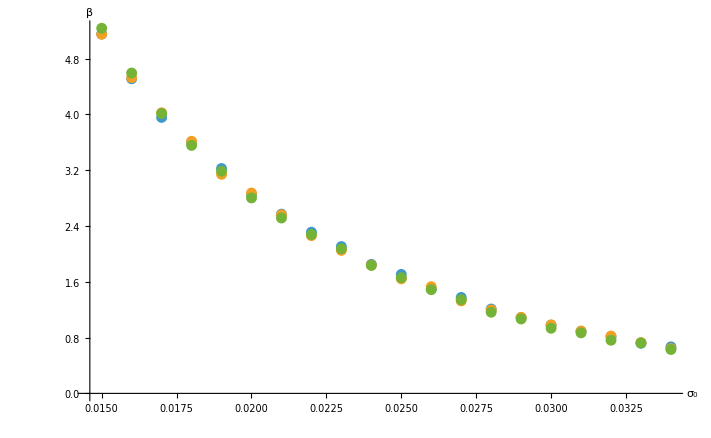

```mathematica
ListPlot[{Transpose[{Array[0.014+#*0.001&,20],betas2}],Transpose[{Array[0.014+#*0.001&,20],betas3}],Transpose[{Array[0.014+#*0.001&,20],betas4}]},
AxesLabel->{"σ_0","β"},LabelStyle->Directive[Bold]]
```

### Estimation of beta Brody

```mathematica
betas2Brody={};
For[j=11,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.03+j*0.01)/Sqrt[i]],1] /.l->i /. d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];

AppendTo[betas2Brody,Values[fit["BestFitParameters"]][[1]]];
Echo[betas2Brody]
]
Export["BETA_SIGMA0_d2_Brody.dat",Transpose[{Array[0.014+#*0.001&,20],betas2Brody}]]
```

Transpose::nmtx: The first two levels of {{0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034},{0.105716,0.0897699,0.0872428,0.0812559,0.0753822,0.0661168,0.0675507,0.0585165,0.0585009,0.0511951}} cannot be transposed.

BETA_SIGMA0_d2_Brody.dat

```mathematica
betas3Brody={};
For[j=11,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.030+j*0.01)/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];

AppendTo[betas3Brody,Values[fit["BestFitParameters"]][[1]]];
Echo[betas3Brody]
]
Export["BETA_SIGMA0_d3_Brody.dat",Transpose[{Array[0.014+#*0.001&,20],betas3Brody}]]
```

Transpose::nmtx: The first two levels of {{0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034},{0.0999999,0.0912326,0.0886193,0.0799496,0.0816012,0.0738704,0.0678594,0.0606256,0.0542831,0.0540788}} cannot be transposed.

BETA_SIGMA0_d3_Brody.dat

```mathematica
betas4Brody={};
For[j=11,j<=20,j++,
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.03+j*0.01)/Sqrt[i]],1] /.l->i /. d->4,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];

AppendTo[betas4Brody,Values[fit["BestFitParameters"]][[1]]];
Echo[betas4Brody]
]
Export["BETA_SIGMA0_d4_Brody.dat",Transpose[{Array[0.014+#*0.001&,20],betas4Brody}]]
```

Transpose::nmtx: The first two levels of {{0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034},{0.10717,0.101599,0.0876007,0.0855446,0.0785079,0.0645586,0.0622501,0.0606993,0.0557779,0.0597695}} cannot be transposed.

BETA_SIGMA0_d4_Brody.dat

### SFF

```mathematica
Quit[];
```

```mathematica
CumulativeSFFLIST=0;
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
T=logspace[7,13,1000];
```

```mathematica
CumulativeSFFLIST=0;
For[j=1,j<=20,j++,
OmegaQuantizationSFF={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.5/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationSFF,Value[[1]]];
];

SFF[tn0_]=Abs[Total[Exp[ⅈ*tn0*OmegaQuantizationSFF]]/400]^2;
SFFLIST=Parallelize[Table[{tn,SFF[tn]},{tn,T}]];
CumulativeSFFLIST+=SFFLIST;
Echo[CumulativeSFFLIST[[1]]]
]
SFFMEAN=CumulativeSFFLIST/20;
Speak["Finish"]
```

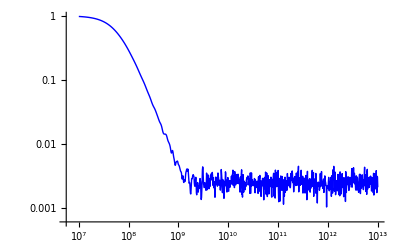

```mathematica
ListPlot[SFFMEAN,PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->All,Joined->True]
```

```mathematica
Export["SFF_STATIC_SIGMA05.dat",SFFMEAN]
```

SFF_STATIC_SIGMA05.dat

### Functions

```mathematica
GSE=Table[{x,p[x,4]/.α->1},{x,0,4,0.01}];
```

```mathematica
Export["GSE.dat",GSE]
```

GSE.dat

```mathematica
GUE=Table[{x,p[x,2]/.α->1},{x,0,4,0.01}];
```

```mathematica
Export["GUE.dat",GUE]
```

GUE.dat

```mathematica
GOE=Table[{x,p[x,1]/.α->1},{x,0,4,0.01}];
```

```mathematica
Export["GOE.dat",GOE]
```

GOE.dat

```mathematica
POISSON=Table[{x,Exp[-x]},{x,0,4,0.01}];
```

```mathematica
Export["POISSON.dat",POISSON]
```

POISSON.dat

```mathematica
d2={1.070461889338368,0.6419035408682789,0.4197443299513286,0.32903023791065517,0.2605483821876933,0.21163868064953367,0.1767272288348319,0.15838514001997472,0.14529092848665162,0.12220867740708703,0.12309990156461943,0.10571607336099076,0.08976988620225697,0.08724284294671594,0.08125587489713491,0.07538216432780356,0.06611679487481191,0.06755065587916988,0.05851646914371101,0.05850094221898236,0.051195117739545354}
```

{1.07046,0.641904,0.419744,0.32903,0.260548,0.211639,0.176727,0.158385,0.145291,0.122209,0.1231,0.105716,0.0897699,0.0872428,0.0812559,0.0753822,0.0661168,0.0675507,0.0585165,0.0585009,0.0511951}

```mathematica
d3={1.0882302110733508,0.6399937736923776,0.4198703547914841,0.3228045894914325,0.24480641597324307,0.21760753870993585,0.1684147423528505,0.15080928838219856,0.1388789938723177,0.12233220964582374,0.11239670470949234,0.09999988837735908,0.09123258743213075,0.08861933919430426,0.07994958421518489,0.08160124389770712,0.07387037309985878,0.06785943022088044,0.06062555930980763,0.05428313779057074,0.054078754297288416}
```

{1.08823,0.639994,0.41987,0.322805,0.244806,0.217608,0.168415,0.150809,0.138879,0.122332,0.112397,0.0999999,0.0912326,0.0886193,0.0799496,0.0816012,0.0738704,0.0678594,0.0606256,0.0542831,0.0540788}

```mathematica
d4={1.0851192856171725,0.643750860215339,0.4307908156454329,0.3269481103103802,0.2496406164408059,0.21418480051265754,0.1735674725203233,0.1515604459767594,0.13735928672121278,0.12764072358974968,0.10806170398994674,0.1071697785149893,0.10159869897087993,0.08760067351932913,0.08554456779298461,0.07850791167121761,0.06455859308662497,0.06225005345279519,0.06069933478819342,0.05577790268293388,0.059769478620794465}
```

{1.08512,0.643751,0.430791,0.326948,0.249641,0.214185,0.173567,0.15156,0.137359,0.127641,0.108062,0.10717,0.101599,0.0876007,0.0855446,0.0785079,0.0645586,0.0622501,0.0606993,0.0557779,0.0597695}

```mathematica
Array[0.03+#*0.01&,20]
```

{0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.12,0.13,0.14,0.15,0.16,0.17,0.18,0.19,0.2,0.21,0.22,0.23}

```mathematica
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.03/Sqrt[i]],1] /.l->i /. d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];
Echo[Values[fit["BestFitParameters"]][[1]]]
```

1.07046

```mathematica
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.03/Sqrt[i]],1] /.l->i /. d->3,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];
Echo[Values[fit["BestFitParameters"]][[1]]]
```

1.08823

```mathematica
cumulativebinCounts=0;
For[n=1,n<=200,n++,
OmegaQuantizationBeta={};
For[i=1, i<=400, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.03/Sqrt[i]],1] /.l->i /. d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantizationBeta,Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta]];
spline[x_]=Function[x,Fit[Transpose[{Sort[OmegaQuantizationBeta],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[Sort[OmegaQuantizationBeta]];
spacings=Differences[unfoldedE];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
cumulativebinCounts +=binCounts;

Echo[j.n]
];
binCounts = cumulativebinCounts/200;

fit= NonlinearModelFit[Transpose[{{0.05,0.15,0.25,0.35,0.45,0.55,0.65,0.75,0.85,0.95,1.05,1.15,1.25,1.35,1.45,1.55,1.65,1.75,1.85,1.95,2.05,2.15,2.25,2.35,2.45,2.55,2.65,2.75,2.85,2.95,3.05,3.15,3.25,3.35,3.45,3.55,3.65,3.75,3.85,3.95},binCounts}],p[s, β]/.α->β//FullSimplify,β,s];
Echo[Values[fit["BestFitParameters"]][[1]]]
```

1.08512

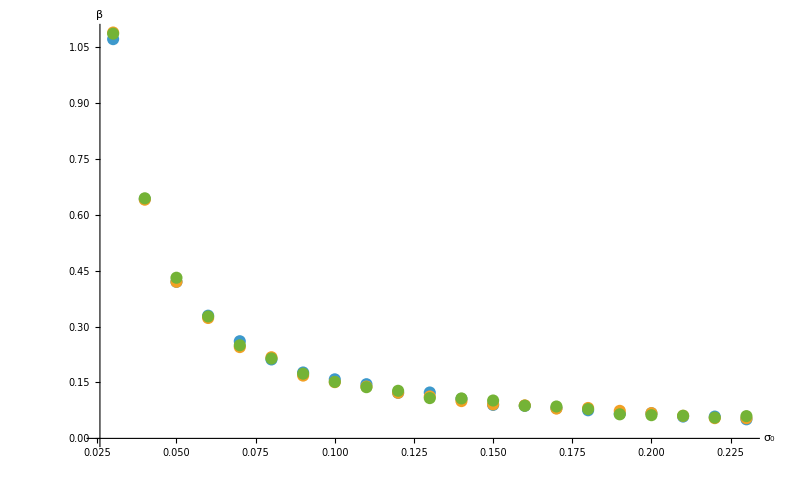

```mathematica
ListPlot[{Transpose[{Array[0.02+#*0.01&,21],d2}],Transpose[{Array[0.020+#*0.01&,21],d3}],Transpose[{Array[0.020+#*0.01&,21],d4}]},
AxesLabel->{"σ_0","β"},LabelStyle->Directive[Bold],PlotRange->All]
```

```mathematica
Export["BETA_SIGMA0_d4_Brody.dat",Transpose[{Array[0.02+#*0.01&,21],d4}]]
```

BETA_SIGMA0_d4_Brody.dat